### NDSolve Module

```mathematica
solvestep[L_,t0_,θ0_,ϕ0_,α0_,dθ0_,dϕ0_,dα0_,tguess_,tf_, constraints_]:=(
(*Add the constraints*)
L1=L;
For[i=1,i≤ Length[constraints],i++,
L1=L1+constraints[[i]][[1]] constraints[[i]][[2]];];
sol= {};
(*NDSolve based on how many constraints*)
Which[Length[constraints]==2,
sol=NDSolve[{EL[L1,θ],EL[L1,ϕ],EL[L1,α],
α[t0]==α0,
α'[t0]==dα0,
θ[t0]==θ0,
θ'[t0]==dθ0,
ϕ[t0]==ϕ0,
ϕ'[t0]==dϕ0,
D[constraints[[1,2]],t,t]==0,
D[constraints[[2,2]],t,t]==0},
{θ[t],ϕ[t],α[t],constraints[[1,1]],constraints[[2,1]]},{t,t0,tf}],
Length[constraints]==1,
sol = NDSolve[{EL[L1,θ],EL[L1,ϕ],EL[L1,α],
α[t0]==α0,
α'[t0]==dα0,
θ[t0]==θ0,
θ'[t0]==dθ0,
ϕ[t0]==ϕ0,
ϕ'[t0]==dϕ0,
D[constraints[[1,2]],t,t]==0},
{θ[t],ϕ[t],α[t],constraints[[1,1]]},{t,t0,tf}],
Length[constraints]==0,
sol = NDSolve[{EL[L1,θ],EL[L1,ϕ],EL[L1,α],
α[t0]==α0,
α'[t0]==dα0,
θ[t0]==θ0,
θ'[t0]==dθ0,
ϕ[t0]==ϕ0,
ϕ'[t0]==dϕ0},
{θ[t],ϕ[t],α[t]},{t,t0,tf}]];
(*Pull off solutions*)
solnlist = {};
For[i = 1, i≤Length[sol[[1]]],i++,
AppendTo[solnlist, sol[[1,i,2]]]; 
];
(*Obtain first zeros*)
zeros={};
For[i=4, i≤Length[solnlist],i++,
AppendTo[zeros,
FindRoot[solnlist[[i]],{t,tguess}]];
];
(*Return solutions and zeros*)
Return[{solnlist,zeros}];
)
```

## Kinetic energy

```mathematica
Clear[T,U,mb,mcw,ma,IIa,l1,l2,h,r,g,θ,ϕ,α,L,t,tf,EL,soln,xb,yb,xcw,ycw,xcma,ycma,λ,γ,G1,G2,x,y]
```

```mathematica
T:= 1/2 mb(D[xb,t]^2+D[yb,t]^2) + 1/2 mcw(D[xcw,t]^2+D[ycw,t]^2)+1/2 IIa D[θ[t],t]^2
```

Note, if you call moment of inertia I you generate errors because this is the imaginary number

```mathematica
IIa:=1/3 ma ((l1^3+l2^3)/(l1+l2))
```

### Potential energy

```mathematica
U:= mb g yb+mcw g ycw+ma g ycma
```

### Define transformation to generalized coordinates

```mathematica
xb:= l1 Cos[θ[t]]+r Cos[ϕ[t]](*these are barrel coord*)
yb:=-l1 Sin[θ[t]]-r Sin[ϕ[t]]
xcw:=-l2 Cos[θ[t]]+h Cos[α[t]](*these are counter-weight coord*)
ycw:=l2 Sin[θ[t]]-h Sin[α[t]]
ycma:=-(l1-l2)/2 Sin[θ[t]](*these are center of mass coord*)
```

### Define Constraint Functions:

```mathematica
G1:= θ[t]-α[t]+α[0](*counter weight*)
```

```mathematica
G2:=θ[t]-ϕ[t]+ϕ[0](*barrel*)
```

Let' s see what T & U look like ... It looks nice.  Doing this in Mathematica saves the pain of differentiating, squaring etc.  Try a few lines of this to get a feel for how nasty it is.

```mathematica
Simplify[T]
```

1/6 (3 h^2 mcw α'[t]^2-6 h l2 mcw Cos[α[t]-θ[t]] α'[t] θ'[t]+(-l1 l2 ma+l1^2 (ma+3 mb)+l2^2 (ma+3 mcw)) θ'[t]^2+6 l1 mb r Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+3 mb r^2 ϕ'[t]^2)

```mathematica
Simplify[U]
```

-1/2 g (2 h mcw Sin[α[t]]+(l1 (ma+2 mb)-l2 (ma+2 mcw)) Sin[θ[t]]+2 mb r Sin[ϕ[t]])

#### Define L

```mathematica
L:= T - U
```

```mathematica
Simplify[L]
```

1/6 (3 h^2 mcw α'[t]^2-6 h l2 mcw Cos[α[t]-θ[t]] α'[t] θ'[t]+(-l1 l2 ma+l1^2 (ma+3 mb)+l2^2 (ma+3 mcw)) θ'[t]^2+6 l1 mb r Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+3 (g (2 h mcw Sin[α[t]]+(l1 (ma+2 mb)-l2 (ma+2 mcw)) Sin[θ[t]]+2 mb r Sin[ϕ[t]])+mb r^2 ϕ'[t]^2))

```mathematica
g:=9.81
mb:=60
mcw:=3000
ma:=1000
l1:=10
l2:=4
h:=10
r:=6
```

```mathematica
EL[L_,x_] :=D[L,x[t]]-D[L,x'[t],t]==0;
```

```mathematica
Clear[L1,solnlist,zeros,sol,constraints1, tf];
```

```mathematica
tf=20;
```

```mathematica
constraints1={{λ[t],G1},{γ[t],G2}};
```

```mathematica
step1 = solvestep[L,0,0,Pi,7Pi/4,0,0,0,1,tf,constraints1]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{{t→1.19494},{t→1.70667}}}

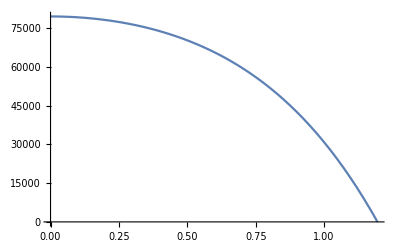

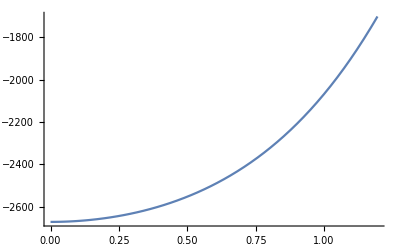

```mathematica
Plot[step1[[1,4]],{t,0,t2}]
Plot[step1[[1,5]],{t,0,t2}]
```

```mathematica
Print[step1[[2]]]
```

{{t→1.19494},{t→1.70667}}

```mathematica
Clear[L2,solnlist,zeros,constraints2,sol,t2,step2];
```

```mathematica
constraints2={{γ[t],G2}};
```

```mathematica
t2=step1[[2,1,1,2]];
Print[t2];
```

1.19494

```mathematica
step2 = solvestep[L,t2,step1[[1,1,0]][t2],step1[[1,2,0]][t2],step1[[1,3,0]][t2],step1[[1,1,0]]'[t2],step1[[1,2,0]]'[t2],step1[[1,3,0]]'[t2],2,tf, constraints2]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

InterpolatingFunction::dmval: Input value {1.11095} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.17022} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{InterpolatingFunction[{{1.19494, 20.}}, <>][t],InterpolatingFunction[{{1.19494, 20.}}, <>][t],InterpolatingFunction[{{1.19494, 20.}}, <>][t],InterpolatingFunction[{{1.19494, 20.}}, <>][t]},{{t→1.43735}}}

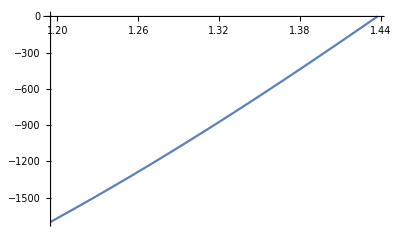

```mathematica
Plot[step2[[1,4]],{t,t2,t3}]
```

```mathematica
Print[step2[[2]]]
```

{{t→1.43735}}

```mathematica
Clear[L1,solnlist,zeros,constraints3,sol,t3];
```

```mathematica
constraints3={};
```

```mathematica
t3=step2[[2,1,1,2]];
Print[t3]
```

1.43735

```mathematica
step3 = solvestep[L,t3,step2[[1,1,0]][t3],step2[[1,2,0]][t3],step2[[1,3,0]][t3],step2[[1,1,0]]'[t3],step2[[1,2,0]]'[t3],step2[[1,3,0]]'[t3],2,tf, constraints3]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{}}

```mathematica
Clear[L1,solnlist,zeros,constraints4,sol,t4];
```

```mathematica
t4=FindRoot[Sin[step3[[1,1]]]==-1,{t,1.7}][[1,2]]
```

InterpolatingFunction::dmval: Input value {-0.726836} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-0.726836

```mathematica
θstop =step3[[1,1,0]][t4]
```

InterpolatingFunction::dmval: Input value {-0.726836} lies outside the range of data in the interpolating function. Extrapolation will be used.

-2.77746×10^14

```mathematica
G3:=θ[t]-θ[t4];
```

```mathematica
constraints4={{β[t],G3}};
```

```mathematica
step4=solvestep[L,t4,step3[[1,1,0]][t4],step3[[1,2,0]][t4],step3[[1,3,0]][t4],0,step3[[1,2,0]]'[t4],step3[[1,3,0]]'[t4],2,tf, constraints4]
```

InterpolatingFunction::dmval: Input value {-0.726836} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{}⟦1,1,2⟧,{}⟦1,2,2⟧},{}}

```mathematica
θpw[t_]=Piecewise[{{step1[[1,1]], 0≤t≤t2}, {step2[[1,1]], t2≤t≤t3}, {step3[[1,1]], t3≤t≤tf}}];
```

```mathematica
ϕpw[t_]=Piecewise[{{step1[[1,2]], 0≤t≤t2}, {step2[[1,2]], t2≤t≤t3}, {step3[[1,2]], t3≤t≤tf}}];
```

```mathematica
αpw[t_]=Piecewise[{{step1[[1,3]], 0≤t≤t2}, {step2[[1,3]], t2≤t≤t3}, {step3[[1,3]], t3≤t≤tf}}];
```

```mathematica
λpw[t_]=Piecewise[{{step1[[1,4]], 0≤t≤t2}, {0, t2≤t≤t3}, {0, t3≤t≤tf}}];
```

```mathematica
γpw[t_]=Piecewise[{{step1[[1,5]], 0≤t≤t2}, {step2[[1,4]], t2≤t≤t3}, {0, t3≤t≤tf}}];
```

```mathematica
θpw[0]
```

6.92981×10^-15

```mathematica
θpw[tf]
```

13.4246

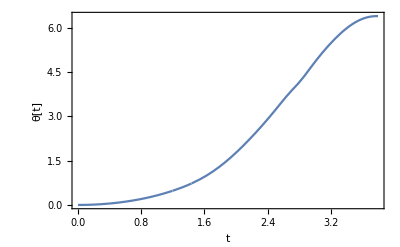

```mathematica
Plot[θpw[t],{t,0,tlaunch +1},PlotRange->All,Frame->True,FrameLabel->{"t","θ[t]","Throwing Arm Angle"}]
(*Plot[θpw'[t],{t,0,tf},PlotRange->All,Frame->True,FrameLabel->{"t","θ'[t]","Throwing Arm Angular Velocity"}]*)
```

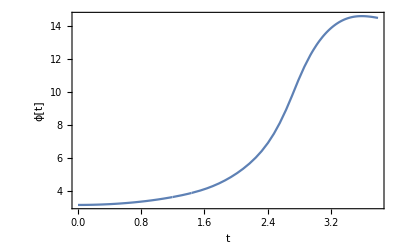

```mathematica
Plot[ϕpw[t],{t,0,tlaunch + 1},PlotRange->All,Frame->True,FrameLabel->{"t","ϕ[t]","Sling Angle"}]
(*Plot[ϕpw'[t],{t,0,tf},PlotRange->All,Frame->True,FrameLabel->{"t","ϕ'[t]","Sling Angular Velocity"}]*)
```

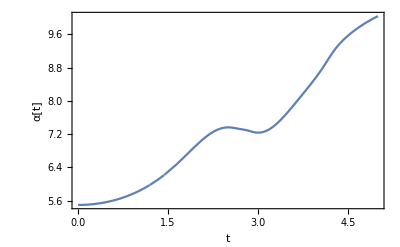

```mathematica
Plot[αpw[t],{t,0,5},PlotRange->All,Frame->True,FrameLabel->{"t","α[t]","CW Arm Angle"}]
(*Plot[αpw'[t],{t,0,tf},PlotRange->All,Frame->True,FrameLabel->{"t","α'[t]","CW Arm Angular Velocity"}]*)
```

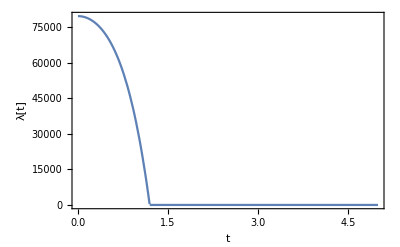

```mathematica
Plot[λpw[t],{t,0,5},PlotRange->All,Frame->True,FrameLabel->{"t","λ[t]","CW Constraint Force"}]
```

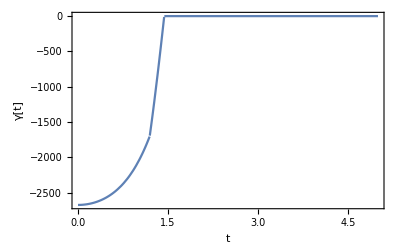

```mathematica
Plot[γpw[t],{t,0,5},PlotRange->All,Frame->True,FrameLabel->{"t","γ[t]","Sling Constraint Force"}]
```

```mathematica
xtapp[t_]=l1 Cos[θpw[t]];
ytapp[t_]=-l1 Sin[θpw[t]];
xtacp[t_]=-l2 Cos[θpw[t]];
ytacp[t_]=l2 Sin[θpw[t]];
```

```mathematica
xbp[t_]= l1 Cos[θpw[t]]+r Cos[ϕpw[t]];(*these are barrel coord*)
ybp[t_]=-l1 Sin[θpw[t]]-r Sin[ϕpw[t]];
xcwp[t_]=-l2 Cos[θpw[t]]+h Cos[αpw[t]];(*these are counter-weight coord*)
ycwp[t_]=l2 Sin[θpw[t]]-h Sin[αpw[t]];

Clear[x,y,xdrag,ydrag];
tlaunch=FindRoot[xbp'[t]==ybp'[t],{t,2.74}][[1,2]];
b=0;
dragsoln=NDSolve[{
xdrag[tlaunch]==xbp[tlaunch],
ydrag[tlaunch]==ybp[tlaunch],
xdrag'[tlaunch]==xbp'[tlaunch],
ydrag'[tlaunch]==ybp'[tlaunch],
xdrag''[t]==-b/mb xdrag'[t],
ydrag''[t]==-b/mb ydrag'[t]-g },
{xdrag,ydrag} ,{t,tlaunch,tf}];
xd=dragsoln[[1,1,2]];
yd=dragsoln[[1,2,2]];

xbtotal[t_]=Piecewise[{{xbp[t], 0≤t≤tlaunch}, {xd[t], tlaunch<t≤tf}}];
ybtotal[t_]=Piecewise[{{ybp[t], 0≤t≤tlaunch}, {yd[t], tlaunch<t ≤tf}}];
```

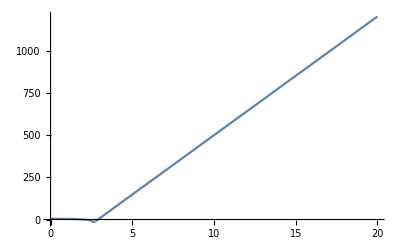

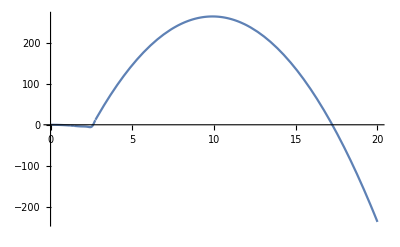

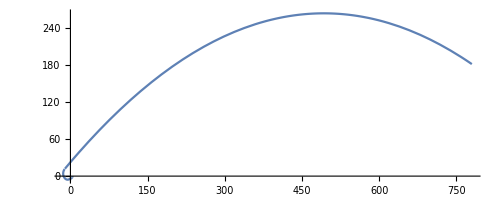

```mathematica
Plot[xbtotal[t],{t,0,tf}]
Plot[ybtotal[t],{t,0,tf}]
ParametricPlot[{xbtotal[t],ybtotal[t]},{t,0,14}]
```

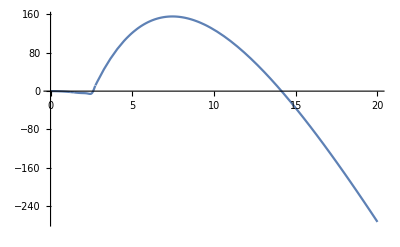

-Graphics-

```mathematica
Manipulate[Graphics[{
Line[{{-12,-12},{-12,12}}],
Line[{{-12,12},{12,12}}],
Blue,Line[{{xtapp[t],ytapp[t]},{xtacp[t],ytacp[t]}}],
Black,Line[{{xtapp[t],ytapp[t]},{xbp[t],ybp[t]}}],
Red,Line[{{xtacp[t],ytacp[t]},{xcwp[t],ycwp[t]}}],
Black,Line[{{-8,-8},{0,0}}],
Black,Line[{{0,0},{8,-8}}],
Black,Line[{{-8,-8},{8,-8}}],
Red,Rectangle[{xcwp[t]-.5,ycwp[t]-.5},{xcwp[t]+.5,ycwp[t]+.5}],
Darker[Green], Disk[{xbtotal[t],ybtotal[t]},.5]

},ImageSize->Large],
{t,0.0000,14}]
```

```mathematica
Manipulate[Graphics[{
Line[{{-6,-6},{-6,55}}],
Line[{{-6,55},{350,55}}],
Blue,Line[{{xtapp[t],ytapp[t]},{xtacp[t],ytacp[t]}}],
Black,Line[{{xtapp[t],ytapp[t]},{xbp[t],ybp[t]}}],
Red,Line[{{xtacp[t],ytacp[t]},{xcwp[t],ycwp[t]}}],
Black,Line[{{-4,-6},{0,0}}],
Black,Line[{{0,0},{4,-6}}],
Black,Line[{{-4,-6},{4,-6}}],
Red,Rectangle[{xcwp[t]-.5,ycwp[t]-.5},{xcwp[t]+.5,ycwp[t]+.5}],
Darker[Green], Disk[{xbtotal[t],ybtotal[t]},.5],

},ImageSize->Large],
{t,0.0000,8}]
```

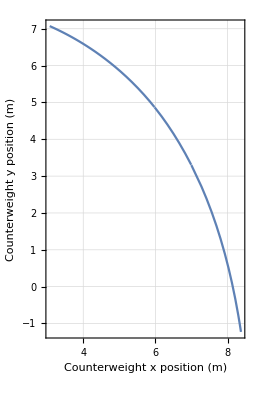

```mathematica
ParametricPlot[{xcwp[t],ycwp[t]},{t,0,1.9},AspectRatio->Full,Frame->True,FrameLabel->{"Counterweight x position (m)","Counterweight y position (m)","Trajectory of Counterweight Swing (Fixed Trebuchet)"}, GridLines->Automatic]
```

```mathematica
Clear[Tpw,Upw,Epw]
```

```mathematica
ycmap[t_]:=-(l1-l2)/2 Sin[θpw[t]];
```

```mathematica
Tpw[t_]= 1/2 mb(D[xbp[t],t]^2+D[ybp[t],t]^2) + 1/2 mcw(D[xcwp[t],t]^2+D[ycwp[t],t]^2)+1/2 IIa D[θpw[t],t]^2;
Upw[t_]=mb g ybp[t]+mcw g ycwp[t]+ma g ycmap[t];
```

```mathematica
Epw[t_]=Tpw[t]+Upw[t];
```

```mathematica
Plot[Epw[t],{t,0,t4},PlotRange->{866,868}]
```

-Graphics-

```mathematica
ttest=FindRoot[xbp'[t]==ybp'[t],{t,1.63}][[1,2]]
```

1.48284

```mathematica
θpw[ttest]+ϕpw[ttest]
```

4.71262

```mathematica
N[17Pi/4]
```

13.3518

```mathematica
Utoti=Upw[0]
```

208102.

```mathematica
Tbf =  1/2 mb(xbp'[ttest]^2+ybp'[ttest]^2)
```

816.115

```mathematica
KineticRatio = Tbf/Utoti
```

0.00392172